# Math 385 HW # 10

## Mario L. Gutierrez Abed

(1) We are given the function u(x)=1-ⅇ^(-x/5) , with x∈[0,20]. Take u(0)=0 and Δ x=2. We need to apply Forward Euler, Forward Euler w/ corrector, Midpoint/Runge, and Taylor method and then plot all on the same graph. 

Solution:
We are given the curve u(x)=1-ⅇ^(-x/5) . 
Consequently, we have
•  u'(x)=1/5 ⅇ^(-x/5)=1/5(1-u)   
•  u''(x)=-1/25 ⅇ^(-x/5)=1/25(u-1)

				        Forward Euler
Applying forward Euler, we can estimate u(x_(i+1)) from each u(x_i). To that end, we use u(x_(i+1))=u(x_i)+f(x_i,u(x_i))(x_(i+1)-x_i),
where f(x_i,u(x_i))=u'(x_i)  and  x_(i+1)-x_i=Δ x .

```mathematica
euler={0};
u1=0;
For[i=2,i≤20,i=i+2,
u1=u1+1/5*(1-u1)*2;
AppendTo[euler,u1]
];
```

Forward Euler corrected	
Just like we did with the forward Euler method, we derive u_1 from u_0 by setting 
 u_1=u_0+u'_0 Δ x
u_1=0+1/5(1-0)·2=2/5
This time however, the remainder of the iterations will be different. We take the corrective derivative at u_1, 
(û')_1≈1/2(u'_1+u'_0)≈1/10((1-u_1)+(1-u_0))
	            ≈1/10((1-(u_0+u'_0 Δ x))+(1-u_0))
	            ≈1/10(2-2 u_0-u'_0 Δ x)
	            ≈1/10(2-2 u_0-1/5(1-u_0)Δ x)
In general we have 
(û')_(i+1)≈1/2(u'_(i+1)+u'_i)≈1/10((1-u_(i+1))+(1-u_i))

We need to solve for u_(i+1) by executing
 u_(i+1)=u_i+(û')_(i+1)(x_(i+1)-x_i)
       =u_i+(û')_(i+1)Δ x
       =u_i+1/10(2-2 u_i-1/5(1-u_i)Δ x)Δ x

```mathematica
ceuler={0,2/5};
u2=2/5;
For[i=4,i≤20,i=i+2,
u2=u2+1/10*(2-2*u2-1/5*(1-u2)*2)*2;
AppendTo[ceuler,u2]
];
```

Taylor method
For the Taylor method we have that the expansion of order 2 of our function is given by 
u(x_(i+1))=u(x_i)+f(x_i,u(x_i))(x_(i+1)-x_i)+1/2 f'(x_i,u(x_i))(x_(i+1)-x_i)^2
or 
             u(x_(i+1))=u(x_i)+u'(x_i)Δ x+1/2 u''(x_i)(Δ x)^2
      ⟹ u(x_(i+1))=u(x_i)+1/5(1-u)·2+1/2[1/25(u-1)·4]
      ⟹ u(x_(i+1))=u(x_i)+2/5(1-u)+2/25(u-1)

```mathematica
taylor={0};
u3=0;
For[i=2,i≤20,i=i+2,
u3=u3+2/5*(1-u3)+2/25*(u3-1);
AppendTo[taylor,u3]
];
```

Midpoint/Runge method
For the Runge method we take ξ_i=1/2(x_(i+1)+x_i), which is the midpoint for each subinterval [x_i,x_(i+1)]. Then we need to execute 
u(x_(i+1))=u(x_i)+f(ξ_i,u(ξ_i))(x_(i+1)-x_i)
or 
u(x_(i+1))=u(x_i)+u'(ξ_i)Δ x

Now we have that u(ξ_i) is estimated by
 u(ξ_i)=u(x_i)+1/2 f(x_i,u(x_i))(x_(i+1)+x_i) or 
 u(ξ_i)=u(x_i)+1/2 u'(x_i)Δ x
Hence
       u'(ξ_i)=u'(x_i)+1/2 u''(x_i)Δ x
⟹ u'(ξ_i)=1/5(1-u)+1/2·1/25(u-1)Δ x
                =1/5(1-u)+1/50(u-1)Δ x

Thus, we have
u(x_(i+1))=u(x_i)+u'(ξ_i)Δ x
          =u(x_i)+(1/5(1-u)+1/50(u-1)Δ x)Δ x
          =u(x_i)+1/5(1-u)Δ x+1/50(u-1)(Δ x)^2
Let’s get on with the computations:

```mathematica
runge={0};
u4=0;
For[i=2,i≤20,i=i+2,
u4=u4+1/5*(1-u4)*2+1/50(u4-1)*4;
AppendTo[runge,u4]
];
```

RESULTS
Now let us plot our function and all the approximations...

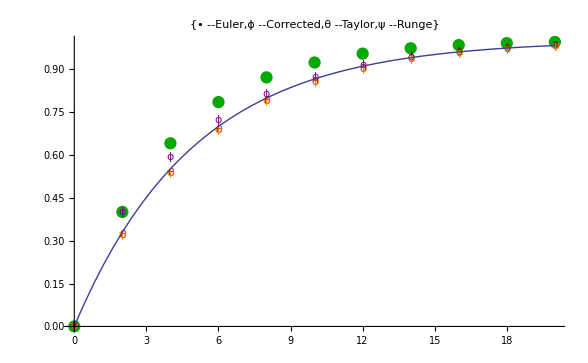

```mathematica
curve[x_]=1-ⅇ^(-x/5);
curveplot=Plot[curve[x],{x,0,20},PlotLabel->"Yo"];
eulerplot=ListPlot[euler,DataRange->{0,20},PlotStyle->{Darker[Green],PointSize[0.015]}];
correctedplot=ListPlot[ceuler,DataRange->{0,20},PlotMarkers->ϕ,PlotStyle->Purple];
taylorplot=ListPlot[taylor,DataRange->{0,20},PlotMarkers->θ,PlotStyle->{Darker[Red],PointSize[0.015]}];
rungeplot=ListPlot[runge,DataRange->{0,20},PlotMarkers->ψ,PlotStyle->{Orange,PointSize[0.015]}];
Show[{eulerplot,correctedplot,taylorplot,rungeplot,curveplot},PlotLabel->{Style[Framed["• --Euler"],Darker[Green]],Style[Framed["ϕ --Corrected"],Purple],Style[Framed["θ --Taylor"],Darker[Red]],Style[Framed["ψ --Runge"],Orange]}]
```

Just as expected the most accurate methods were Runge’s and the second order Taylor, followed by the corrected Euler method. The least accurate approximation is the latter without the correction.